# The Development of Quantization

## Purpose

The purpose of this lesson is to...

introduce the idea of quantized states, meaning that a variable (for example, the energy) can only take on certain values.

present the observation that light behaves as both a wave and as a particle (the photon) and that the same is true for matter (atoms and molecules).

discuss the relationship between reciprocal variables for waves and how this property gives rise to the Heisenberg uncertainty principle.

provide a brief discussion of the meaning of uncertainty.

## Learning Objectives

At the end of this lesson, I should be able to...

describe the experiment and theory that led to the establishment of quantum theory.

recall the wave/particle duality for both light and matter, as developed by Einstein and de Broglie, respectively.

explain the relationship between reciprocal variables such as position and momentum and its importance in the Heisenberg uncertainty principle.

## Review: Light as a Wave

We’ll be discussing light quite a bit at the beginning of this course, so let’s take a moment to review the “classical” description of light as a wave that was known at the beginning of the 20^th century. Light can be understood as an electromagnetic wave traveling through space (we’ll find out more about the particle nature of light in a moment). It has an electric field vector E and a magnetic field vector B that oscillate perpendicular to one another. Figure 1.1 shows an illustration for linearly polarized light.

```mathematica
Import["https://upload.wikimedia.org/wikipedia/commons/0/0a/Electromagnetic_wave.png",ImageSize->3000]
```

-Graphics-

Figure 1.1. P.wormer - Electromagnetic Wave - https://upload.wikimedia.org/wikipedia/commons/0/0a/Electromagnetic_wave.png - CC BY-SA 3.0

The speed of light was found to be a constant c (2.998 × 10^8 m s^(−1)), with the frequency ν and wavelength λ of the electromagnetic wave related to the speed by the equation

c=νλ

In this wave-only picture, the energy of light was related to the amplitude of the wave, but this formulation alone wasn’t sufficient to explain some experimental results.

## The Ultraviolet Catastrophe

### A Blackbody

By 1900, people realized there was a big problem with many  classical  theories. One of the prominent mysteries was the emission of light from a “blackbody”. A blackbody is an object that absorbs all radiation (light) incident on it (see Figure 1.2). They also emit thermal radiation (light) from the conversion of thermal energy into electromagnetic energy. The frequency of light emitted is dependent on the temperature of the blackbody. It was known from experiment that there was a maximum in the emission spectra that blue-shifted (decreased in wavelength) as the temperature increased. However, using classical mechanics (the Rayleigh-Jeans law), no maximum was predicted. Instead, spectral intensity was expected to increase with decreasing wavelength.

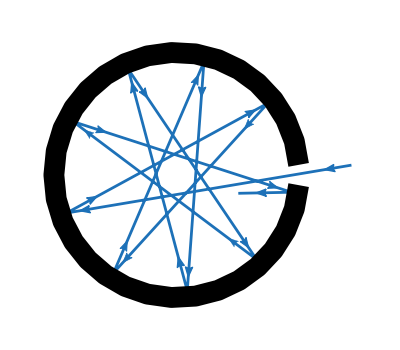

```mathematica
ResourceFunction["SVGImport"]["https://upload.wikimedia.org/wikipedia/commons/d/d8/Black_body_realization.svg"]
```

Figure 1.2. An idealized blackbody, AG Caesar, Wikimedia Commons, CC BY-SA 4.0, https://upload.wikimedia.org/wikipedia/commons/d/d8/Black_body_realization.svg

### The Rayleigh-Jeans Law (Spectral Radiance)

The Rayleigh-Jeans law gives the dependence of light emission B on wavelength λ and temperature T,

B(λ,T) = (2c k_B T)/λ^4

Notice that as λ → 0, B_λ(T) → ∞, which gives unphysical infinite emission of short-wavelength (high-energy) light. The Rayleigh-Jeans law is depicted as the red curve in Figure 1.3.

### Planck’s Law

To address the “ultraviolet catastrophe”, Planck proposed that the energies of the oscillating electrons that yielded radiation (light) could only take on specific values (rather than continuous values):

E = nhν

where n is an integer value, h is a constant known as Planck’s constant, and ν is the light frequency. Planck then derived the following equation for the spectral radiance (known as Planck’s law) :

B(λ,T) = (2 hc^2)/λ^5(1/(e^((h c)/(λ k_B T))-1))

this equation accurately reproduced experimental data, with a value for h

h = 6.626 × 10^(−34) J s

this value is known as Planck’s constant and will pop up just about everywhere. This  result was one of the first breakthroughs showing quantization in physical systems.

### Comparing Rayleigh-Jeans and Planck’s Law

Below you can compare the Rayleigh-Jeans law prediction (red) and the Planck’s Law prediction (blue). Only the Planck’s law equation reproduces experimental data.

```mathematica
Manipulate[
c=3*^8 (*speed of light, m/s*);
kB=1.3806*^-23 (*Boltzmann constant J K-1*);
h=6.626*^-34 (*Planck's constant, m^2 kg s-1*);
Plot[{2*c*kB*T/(λ*1*^-9)^4*1*^-9*1*^-3,(2*h*c^2/(λ*1*^-9)^5)*1/(Exp[h*c/(λ*1*^-9*kB*T)]-1)*1*^-9*1*^-3},{λ,100,2500},PlotRange->{-T^2.8/10000000000,T^2.8/600000000},
BaseStyle->{FontFamily->"Arial",FontSize->16},PlotStyle->{Red,Blue},Frame->True,FrameLabel->{"λ [nm]",Row[{"Spectral Radiance [kW ",Superscript["sr","-1"]," ",Superscript["m","-2"]," ", Superscript["nm","-1"],"]"}]},FrameTicks->{{Automatic,None},{Automatic,None}},ImageSize-> Medium, ImageMargins->{{0,20},{20,20}}
],{{T,5000,"T (K)"},500,8000,Appearance->"Labeled"}]
```

Figure 1.3. Comparison of the Rayleigh-Jeans law prediction (red) and the Planck’s Law prediction (blue).

## The Photoelectric Effect

### Experimental observations

Hertz first reported that ultraviolet light caused electrons to be ejected from metal surfaces.

His student Lennard found that the kinetic energy of the emitted electrons did not depend on the intensity of the light. Increasing the intensity just increased the number of electrons.

Millikan then found that the kinetic energy of the emitted electrons depended on the frequency (energy/color) of the incident light.

Classical theory predicted that electron energy should be proportional to light intensity, not light frequency.

### Photoelectric effect demo

Below is a demo of the photoelectric effect, showing the electrons emitted for various metals, light frequencies, and light intensities.

```mathematica
M[1]="Ag";
M[2]="Al";
M[3]="Au";
M[4]="Ca";
M[5]="Cs";
M[6]="Cu";
M[7]="Fe";
M[8]="K";
M[9]="Mg";
M[10]="Na";
M[11]="Zn";
λ0[1]=1240/4.26 ;λ0[2]=1240/4.28 ;λ0[3]=1240/5.1 ;λ0[4]=1240/2.37 ;λ0[5]=1240/2.14 ;λ0[6]=1240/4.65 ;λ0[7]=1240/4.5 ;λ0[8]=1240/2.3 ;λ0[9]=1240/3.66 ;λ0[10]=1240/2.28 ;λ0[11]=1240/4.3 ;
Int[m_,λ_,int_]:=If[λ≤λ0[m],int,0]
g1[m_,λ_,int_]:=Graphics[{Thick,Line[{{100,0},{0,0},{0,400},{100,400}}],Line[{{100,380},{100,420}}],Line[{{110,395},{110,405}}],Line[{{120,380},{120,420}}],Line[{{130,395},{130,405}}],Line[{{130,400},{500,400},{500,325}}],Black,Rectangle[{450,75},{550,100}],Rectangle[{450,300},{550,325}],Line[{{500,75},{500,0},{200,0}}],Rectangle[{200,155},{350,245}],Polygon[{{350,245},{375,252},{375,148},{350,155}}],
White,EdgeForm[{Thick,Black}],Rectangle[{100,-25},{200,50}],Black,Thickness[.01],Circle[{150,-10},50,{π/4,3π/4}],Thick,Red,Line[{{150,-10},{150+50Cos[π/4+Int[m,λ,int]/100 π/2],-10+50Sin[π/4+Int[m,λ,int]/100 π/2]}}],ColorData["VisibleSpectrum"][λ],EdgeForm[],Opacity[int/100],Polygon[{{375,240},{460,240},{540,160},{375,160},{375,225}}]}]
color[m_]:=Gray;color[3]=RGBColor[1,.843,0];color[6]=RGBColor[1,.5,0];color[8]=color[10]=LightGray;
g2[m_,λ_,int_]:=Graphics[{Blue,Dynamic[Refresh[Point[{Re[#],Im[#]}]&/@RandomComplex[{460+100ⅈ,540+240ⅈ}, Int[m,λ,int]],UpdateInterval->.1]],color[m],Polygon[{{450,300},{550,300},{550,150},{450,250},{450,300}}],Text[Style[M[m],24,White],{500,265}]}]
Manipulate[Show[g1[m,λ,int],g2[m,λ,int],ImageSize->{575,350}],{{m,5,"metal"},{1->"Ag",2->"Al",3->"Au",4->"Ca",5->"Cs",6->"Cu",7->"Fe",8->"K",9->"Mg",10->"Na",11->"Zn"},ControlType->SetterBar},{{λ,550,"wavelength/nm"},50,700,Appearance->"Labeled"},{{int,50,"light intensity"},0,100,1,Appearance->"Labeled"},SaveDefinitions->True]
```

Figure 1.4. Photoelectric effect demonstration. S. M. Blinder (March 2008), CC BY-NC-SA 3.0, Wolfram Demonstrations Project, https://demonstrations.wolfram.com/ThePhotoelectricEffect/

### Einstein’s explanation

Einstein proposed that the energy of the incident light was quantized in packets of energy

E=hν

which we now know as photons. He then proposed that the kinetic energy (KE ) of the emitted electrons is given by

KE = hν−ϕ

where Φ  is the work function of the metal (the minimum energy required to release an electron from that metal). This equation shows how the electron kinetic energy is dependent on the light frequency. In addition, each photon can eject only one electron, so increasing light intensity increases the number of emitted electrons. The combined experiment and theory demonstrated the quantization of light.

Einstein also predicted (to explain the photoelectric effect) that photons have momentum p,

p = h/λ

where λ is the wavelength of the light. How can a massless particle have momentum? That’s something we won’t discuss in this course, but it comes from using  relativity to describe the energy of the photon,

E^2 = (pc)^2+(mc^2)^2

## de Broglie Waves

### de Broglie’s Proposal

de Broglie had the idea to use Einstein’s light proposal (light was a wave that existed in quantized units) in reverse for matter (matter exists in quantized units that are also a wave). He proposed that for matter, just as for light,

p = h/λ

where λ is the de Broglie wavelength. We are more familiar with this equation when we use p = mv  and rearrange to give

λ=h/mv

where m is the particle mass and v is the particle velocity.

### Experimental Observation

Davisson and Germer observed diffraction of electrons from a Nickel surface, thus confirming experimentally de Broglie’s proposal. Their experimental setup is shown in Figure 1.5.

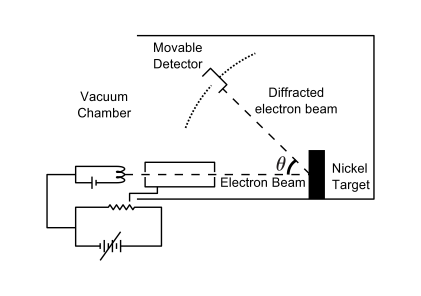

```mathematica
ResourceFunction["SVGImport"]["https://upload.wikimedia.org/wikipedia/commons/4/4e/Davisson-Germer_experiment.svg"]
```

Figure 1.5. Davisson-Germer experimental setup, CC BY-SA 3.0, https://upload.wikimedia.org/wikipedia/commons/4/4e/Davisson-Germer_experiment.svg

The experiments of Davisson and Germer used a fixed scattering angle θ and measured the change in signal on a detector as a function of the accelerating voltage applied to the electrons. Recall that when electrons are passed through a potential of V  volts, they are accelerated to a kinetic energy

E=eV

where e is the charge of an electron = 1.602 × 10^-19 C. Recall also that

E=p^2/(2m)

and that the mass of the electron is 9.109 × 10^-31 kg.

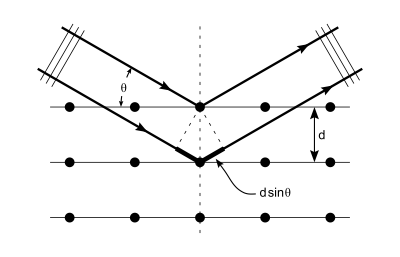

```mathematica
ResourceFunction["SVGImport"]["https://upload.wikimedia.org/wikipedia/commons/c/c0/Bragg_diffraction_2.svg"]
```

Figure 1.6. Bragg Diffraction, Hydrargyrum, Wikimedia Commons, CC BY-SA 3.0, https://commons.wikimedia.org/wiki/File:Bragg_diffraction_2.svg

Constructive interference between waves occurs at the so-called Bragg condition,

nλ=2d sin(θ)

where n is an integer from 1 upwards, d is the lattice spacing (the space between atoms, see image above), and θ is the angle of incidence or angle of scattering (see image above). So if you have a wave incident on the lattice, you can see peaks in the scattering pattern if you scan a detector across the angle of incidence. Because, as de Broglie hypothesized, matter also has a wavelength, diffraction patterns can also be observed for matter.

### The Wave Nature of Matter

The proposal by de Broglie and subsequent experimental verification by Davisson and Germer demonstrated the wave nature of matter (as well as light). Below in Figure 1.7 is a demonstration of the wave nature of the electron. The light areas show the probability of measuring the electron at a specific location at different time points as the electron passes through two slits. This phenomenon leads to a diffraction pattern, typically observed by collection beyond the slit. This is the matter analogue of the famous Young’s double slit experiment for light.

But to really be able to interpret this result, we need to know more about the wave nature of matter. What are its implications? How can we describe it? More on that in the coming lessons.

```mathematica
n=55;dx=1.0/(n-1);hbar=m=1;dt=(m dx^2)/hbar;a=(ⅈ hbar)/dt;b=hbar^2/(4 m dx^2);blist=Table[b,{n-1}];
V=Table[If[0.48<x<0.52&&!(0.4<y<0.475||0.525<y<0.6),10000,0],{y,0,1,dx},{x,0,1,dx}];
Manipulate[
Module[{
psi=Table[Module[{p={x-0.25,y-0.5}},
Exp[ⅈ {100,0}.p-(p.p)/(2 0.14^2)]],{y,0,1,dx},{x,0,1,dx}]},Do[psi=Table[LinearSolve[SparseArray[{Band[{1,2}]->blist,Band[{1,1}]->a-2 b-1/2 V⟦All,j⟧,Band[{2,1}]->blist}],(a+2 b+1/2 V⟦All,j⟧) psi⟦All,j⟧-b Table[psi⟦i,Min[n,j+1]⟧+psi⟦i,Max[1,j-1]⟧,{i,1,n}]],{j,n}];psi=Table[LinearSolve[SparseArray[{Band[{1,2}]->blist,Band[{1,1}]->a-2 b-1/2 V⟦i,All⟧,Band[{2,1}]->blist}],(a+2 b+1/2 V⟦i,All⟧) psi⟦All,i⟧-b Table[psi⟦j,Min[n,i+1]⟧+psi⟦j,Max[1,i-1]⟧,{j,1,n}]],{i,n}],{steps}];
Graphics[Raster[Abs[psi+V]^2,ColorFunction->"ThermometerColors"],ImageSize->{450,450}]],
{{steps,1},1,50,1,Appearance->"Labeled"},
SaveDefinitions->True,
SynchronousUpdating-> False,
ContinuousAction-> False]
```

Table::iterb: Iterator {j,n} does not have appropriate bounds.

Table::iterb: Iterator {i,n} does not have appropriate bounds.

Figure 1.7. Electron passage through two narrow slits. Enrique Zeleny (July 2012), CC BY-NC-SA 3.0, Wolfram Demonstrations Project, https://demonstrations.wolfram.com/ProbabilityDensityForAnElectronPassingThroughTwoNarrowSlits/

## The de Broglie wavelength and the Fourier transform

### The Fourier series - a brief introduction

Let’s say we have a function that exists in the interval from −L to L (these can be any number). Perhaps we don’t know the form of this function, and we want to approximate using some functions that we do know. How could we do that?

We could think of a set of functions, which we will call our basis set, that we could add up to get what we want.

They would need to be “nice” functions, meaning that they don’t have any “jumps” or go to infinity

Fortunately for us, someone already figured out a set of functions that satisfy these requirements. They are the sin() and cos() functions (along with a constant, flat line).
Specifically, we are going to use functions of the form

sin((2πnx)/L)

and

cos((2πnx)/L)

These functions have maxima and minima that are offset from one another, giving us the chance to add them up to form a desired function. We can write this out as

f(x)= 1/2 a_0+∑_(n=1)^∞ a_n cos((2πnx)/L)+∑_(n=1)^∞ b_n sin((2πnx)/L)

where a_0, a_n, and b_n are constants. This is in fact the Fourier series. We won’t go into all of the math, but we even know the values of these constants! In the demonstration shown in Figure 1.8.2, you can see how the goodness of the approximation depends on the number of basis functions n for some typical functions.

```mathematica
Manipulate[
Plot[{PeriodicExtension[k[[1]],x],Evaluate[k[[2]]+Sum[k[[3]] Sin[u x]+k[[4]] Cos[u x],{u,1,m}]]},{x,-r,r},Axes->{True,True}, PlotStyle->{{Thickness[0.003],Black},{Thickness[0.003],Blue}} ,
              Filling->{1->{{2},{Yellow,Orange}}},ImageSize->{500,400},ImagePadding->30],{{k,{Sign,0,1/(Pi*u)*(1-2Cos[u*Pi]+1),0},"function"},{{Sign,0,1/(Pi*u)*(2-2Cos[u*Pi]),0}->"step",{#&,0,2(-1)^(u+1)/u,0}->"sawtooth",
{#^2&,π^2/3,0,(4 (-1)^u)/u^2}->"parabola",
{(#-Pi )(#+Pi)(#-1)&,(2 π^2)/3,(12 (-1)^u)/u^3,-(4(-1)^u)/u^2}->"cubic",
{(Sin[#]UnitStep[#])&,1/Pi,KroneckerDelta[u,1]/2,If[u==1,0,(-(1+(-1)^u)/((-1+u^2) π))]}->"half-wave rectifier"}},
{{m,3,"number of terms"},1,50,1,Appearance->"Labeled"},{{r,Pi,"x range"},Pi,5*Pi,Pi,Appearance->"Labeled"},Initialization:>{(PeriodicExtension[g_,x_]:=If[Abs[x]<Pi,g[x],PeriodicExtension[g,x-2Sign[x]Pi]])}]
```

Figure 1.8. Plot of the Fourier series for various functions. Alain Goriely (March 2011), CC BY-NC-SA 3.0, Wolfram Demonstrations Project, https://demonstrations.wolfram.com/FourierSeriesOfSimpleFunctions/

There’s also Fourier series for complex functions! Now we are going to use a different basis,

cos((2πnx)/L)+ⅈ sin((2πnx)/L)

or, recalling Euler’s formula

ⅇ^(ⅈ(2πnx)/L)

Now we can write the complex Fourier series (for −L/2  to L/2) as

f(x)= ∑_(n=−∞)^∞ A_n ⅇ^(ⅈ(2πnx)/L)

where

A_n = 1/L∫_(−L)^L f(x)e^(−ⅈ(2πnx)/L)dx

You don’t need to worry about the details of this equation, but note that we have a way to calculate what the weighting factors are for each function based on an integral that involves multiplying the function by a complex exponential (which has the form of Euler’s formula).

### From Fourier Series to Fourier Transform

The Fourier series only successfully represents a function on a given interval, but what happens when that interval becomes infinitely large (meaning L→∞)? Now, the A_n values are no longer discrete values but rather a continuous set of values , so

A_n → F(k)dk

Additionally, we are now integrating over the entire range of the function (from −∞ to ∞). Putting all of this together we transform eq. 20 into

f(x)= ∫_(−∞)^∞ F(k)e^(2πikx)dk

The form of our function that describes the weights for our basis now looks like (in analogy to eq. 21)

F(k)=∫_(−∞)^∞ f(x)e^(−2πikx)dx

We call equations (24) and (23), the Fourier transform and inverse Fourier transform, respectively. We will be using a slightly different definition that incorporates a factor of 1/(√(2π)), but the basic form and function of the transform remain the same.

### The meaning of the Fourier transform

The Fourier transform is a mathematical representation encountered in many different applications. It is most often used to change a variable to its reciprocal  to make data more easily interpretable. For example, one can change an intensity vs time graph to an intensity vs. frequency graph, a hugely powerful methodology to deconstruct any process that is periodic in time.

A Fourier transform switches between variables that are inversely related, for example time (units s) and frequency (units s^(−1)). Because of this inverse relationship, you can qualitatively guess that when you narrow the distribution in one space (e.g. time), you broaden it in the other. The Fourier transform lets us evaluate this relationship more quantitatively and also lets us visualize it.

For the relationship between frequency and time, the Fourier transform can be written as

f(ω)=1/(√(2π))∫_(−∞)^∞ f(t)e^(−ⅈωt)dt

where ω is the angular frequency. For a time/frequency Fourier transform, the Fourier transform tells us which wave frequencies to add up to get the observed function in time.

### Using the de Broglie wavelength - transform between position and momentum

Let’s think about the equation for the Fourier transform of position of a wave,

f(ω)=1/(√(2π))∫_(−∞)^∞ f(x)e^(−iωx)dx

It’s important to note here that ω for a wave represented above is related to the wavelength by the equation

ω=(2π)/λ

Also, recall that the wavelength is simply the time spacing of one full cycle of a wave, as shown below for the function Cos(x), which has a wavelength (or period) of 2π.

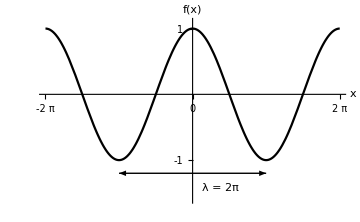

```mathematica
Show[
Plot[Cos[x],{x,-2π,2π},BaseStyle->{FontFamily->"Arial",FontSize->16},PlotStyle->Directive[Black,PointSize[Large]],AxesLabel->{"x","f(x)"},AxesStyle->Directive[Thick,Black],TicksStyle->Directive[Black, Thick],Ticks->{{-4Pi,-2Pi,0,2Pi,4Pi},{-1,1}},PlotRange->{{-2Pi,2Pi},{-1.6,1.1}},ImageSize->Medium,PlotLabels->Placed[{"λ = 2π"},{{1.6,-1.3}}]]
,
Graphics[{Arrowheads[{-.05,.05}],Arrow[{{-Pi,-1.2},{Pi,-1.2}}]}]
]
```

Figure 1.9. Plot of the function cos(x), emphasizing that this function has a wavelength (or period) of 2π.

Ok, so relating that back to de Broglie’s equation, we can now see that, for a matter wave,

p=h/λ=hω/(2π)=ℏω

where we are introducing the new constant (which shows up all the time) ℏ = h/2π. 

How does this relate to the Fourier transform? Well, why don’t we write our Fourier transform as a function of p/ℏ instead of just ω (these two quantities are equal through equation 28),

f(p)=1/(√(2πℏ))∫_(−∞)^∞ f(x)e^(−ⅈpx/ℏ)dx

Wow, did you see that? Now we can see, according to de Broglie’s hypothesis, that there is a reciprocal relationship between position (x) and momentum (p), and this relationship is in fact described by a Fourier transform!

Let’s think about what that means for a minute. In our time/frequency example, the Fourier transform (which gave us a function of frequency) told the weights of frequencies to sum up to generate the observed time distribution. Now, we are talking about momentum/position, so the Fourier transform tells us the weights of momentum values to sum up to get the position distribution. 

We can look at the demonstration of a function and its Fourier transform in Figure 1.10, thinking about position and momentum. You can see that if the position distribution widens, the momentum distribution gets narrower, and vice versa.

```mathematica
f1[yy_,aa_]:=GraphicsRow[{ Plot[1/Sqrt[2 aa] Piecewise[{{0,yy<-aa},{1,yy>-aa&&yy<aa},{0,yy>aa}}],{yy,-5,5},
AxesLabel->{Style["x",24,Italic],Style["f(x)",24,Italic]},PlotStyle->{Thickness[.008],Black},PlotRange->{{-2.2,2.2},{-.1,1.1}},Ticks->{{-2,-1,0,1,2},{0,0.5,1}},TicksStyle->Directive[Gray,20]],
Plot[-(Sin[aa w] (-1+UnitStep[-aa]))/(√aa √π w),{w,-15,15},AxesLabel->{Style["k",24,Red,Italic],Style["f̃(k)",24,Italic,Red]},PlotStyle->{Thickness[.008],Red},PlotRange->{-.5,1},Ticks->{{-10,0,10},{-0.5,0,0.5,1}},TicksStyle->Directive[Gray,20]]}];
f2[yy_,aa_]:=GraphicsRow[{Plot[(2 aa/Pi)^(1/4) Exp[-aa yy^2],{yy,-3.75,3.75},AxesLabel->{Style["x",24,Italic],Style["f(x)",24,Italic]},PlotStyle->{Thickness[.008],Black},PlotRange->{0,1.1},Ticks->{{-3,0,3},{0,0.5,1}},TicksStyle->Directive[Gray,20]],
Plot[(E^(-w^2/(4 aa)))/(aa^(1/4) (2 π)^(1/4)),{w,-7.2,7.2},AxesLabel->{Style["k",24,Red,Italic],Style["f̃(k)",24,Italic,Red]},PlotStyle->{Thickness[.008],Red},PlotRange->{0,1.1},Ticks->{{-6,0,6},{0,0.5,1}},TicksStyle->Directive[Gray,20]]}];
 f3[yy_,aa_]:=GraphicsRow[{Plot[Sqrt[(16 aa^(5/2))/(3 Sqrt[Pi/2])  ] yy^2 Exp[-aa yy^2],{yy,-5,5},AxesLabel->{Style["x",24,Italic],Style["f(x)",24,Italic]},PlotStyle->{Thickness[.008],Black},PlotRange->{-.1,1},Ticks->{{-4,0,4},{0,0.5,1}},TicksStyle->Directive[Gray,20]],
Plot[(√(aa^(5/2)) E^(-w^2/(4 aa)) (2 aa-w^2))/(√3 aa^(5/2) (2 π)^(1/4)),{w,-10,10},AxesLabel->{Style["k",24,Red,Italic],Style["f̃(k)",24,Italic,Red]},PlotStyle->{Thickness[.008],Red},PlotRange->{-.5,1},Ticks->{{-8,0,8},{-0.5,0,0.5,1}},TicksStyle->Directive[Gray,20]]}];
f4[yy_,aa_]:=GraphicsRow[{

Plot[√aa E^(-aa yy) (E^(2 aa yy) HeavisideTheta[-yy]+HeavisideTheta[yy]),{yy,-10,10},AxesLabel->{Style["x",24,Black,Italic],Row[{Style["f(x)",24,Italic,Black]}]},PlotStyle->{Thickness[.008],Black},PlotRange->{0,1.5},Ticks->{{-8,0,8},{0,0.5,1}},TicksStyle->Directive[Gray,20]],

Plot[Sqrt[aa/(2 Pi)] 2 aa/(w^2+aa^2),{w,-10,10},AxesLabel->{Style["k",24,Red,Italic],Style["f̃(k)",24,Italic,Red]},PlotStyle->{Thickness[.008],Red},PlotRange->{{-8.2,8.2},{0,1.2}},Ticks->{{-8,0,8},{0,1,2}},TicksStyle->Directive[Gray,20]]
}];
Manipulate[
Show[ffun[y,a1],ImageSize->{575,400}],

{{ffun,f1,Row[{Style["f",Italic],"(",Style["x",Italic],")"}]},
{f1->"top hat",
f2->Row[{  "exp(","-",Style["a",Italic]," ",Style["x",Italic]^2,")"}],
f3-> Row[{Style[ "x",Italic]^2, "exp(","-",Style["a",Italic]," "," ",Style["x",Italic]^2,")"}],
f4-> Row[{ "exp(","-",Style["a",Italic]," |",Style["x",Italic],"|)"}]}},

{{a1,.5,Style["a",Italic]},.5,2,Appearance->"Labeled"}
,SaveDefinitions->True,TrackedSymbols->True]
```

Figure 1.10. Fourier transform pairs for selected functions. Porscha McRobbie and Eitan Geva (March 2011), CC BY-NC-SA 3.0, Wolfram Demonstrations Project, https://demonstrations.wolfram.com/FourierTransformPairs/

## The Heisenberg Uncertainty Principle

### Statement of the Principle

The idea we’ve been discussing, that the position distribution widens when the momentum distribution gets narrower, is in fact the basic idea of the Heisenberg Uncertainty Principle! More specifically, the principle states

ΔxΔp≥ℏ/2

that is, the uncertainty in the position (Δx) times the uncertainty in the momentum (Δp) cannot be smaller than a constant (ℏ/2). Calculating that constant as ℏ/2 is a bit more involved, and we won’t go through that right now. What’s important now is that you see how position and momentum are inherently related, and you can’t know both at the same time with infinite precision.

### What is the Uncertainty?

In introductory chemistry, the uncertainty in eq. 30 is just explained as the accuracy with which you can measure something. However, the formal definition of Δx or Δp above is the standard deviation of the distribution. Perhaps you’ve heard about standard deviation in a statistics or analytical chemistry course. If not, it is often represented by σ, and (loosely speaking) it is given by

σ^2=(∑(x-x̄)^2)/n

or the square of the standard deviation is equal to the square of the sum over the variation of each point from the mean value (x̄) divided by the number of points. It’s a measure of how far your points are from the average. 

If we know a bit more about our “wave”, then we can in fact calculate the standard deviation, but for now, this just gives you a general idea of what the uncertainty actually refers to.

### Looking Ahead

Up to this point, we’ve talked a lot about “waves” in the most vague sense.

We said that de Broglie proposed particles have some wavelength given by an equation.

We then plugged this into the Fourier transform formula to convert from wavelength (λ) to angular frequency (ω) to momentum (p).

But we haven't said anything about the nature of this wave. Indeed, we haven't said what the wavefunction (the function related to a particle wave) looks like.

That's what Schrödinger (and Heisenberg) discovered, and we’ll be discussing it in the coming lessons